-Graphics-

### Dipole Plots

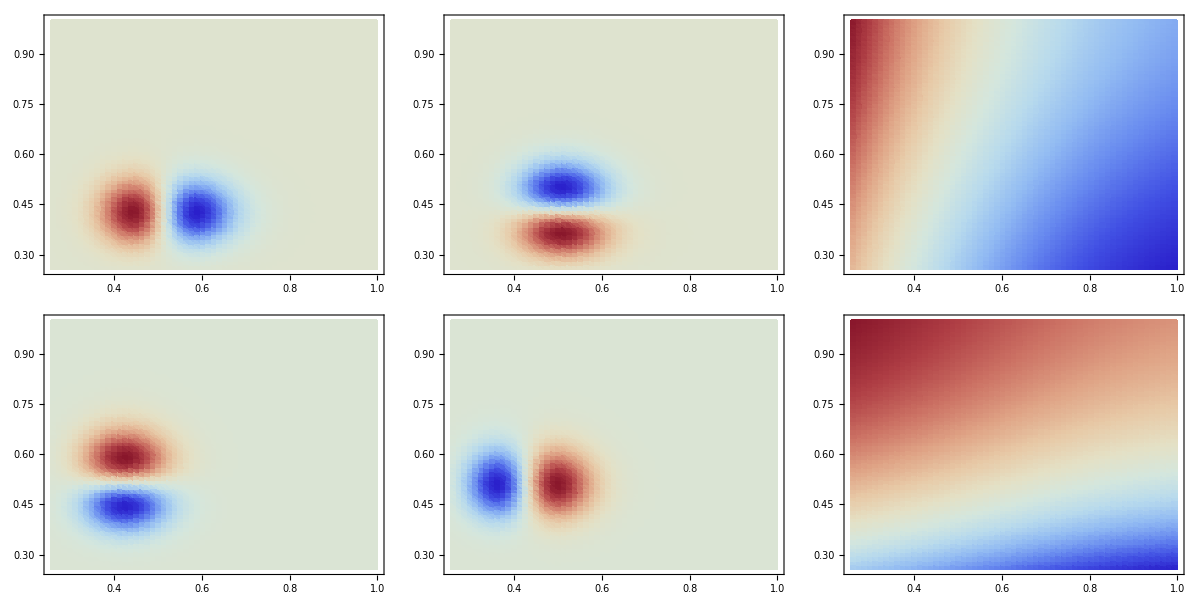

```mathematica
(*Grid@
{
Append[
h2SAWavefunctions[testKey][[{2, 3}]]@
"Plot"["PlotMode"->"Density", "PlotDisplayMode"->List, ColorFunction->"ThermometerColors"],
GridFunctionObject[
h2SAWavefunctions[testKey]["Grid"],
h2SADipoleVectors[testKey]
]@"Plot"["PlotMode"->"Density", ColorFunction->"ThermometerColors"]
],
Append[
h2SAWavefunctions[testKeyInv][[{2, 3}]]@
"Plot"["PlotMode"->"Density", "PlotDisplayMode"->List,ColorFunction->"ThermometerColors"],
GridFunctionObject[
h2SAWavefunctions[testKeyInv]["Grid"],
h2SADipoleVectors[testKeyInv]
]@"Plot"["PlotMode"->"Density", ColorFunction->"ThermometerColors"]
]
}*)
```

```mathematica
makeDipolePlots[key_]:=
With[
{
texture=
GridFunctionObject[
h2SAWavefunctions[key]["Grid"],
h2SADipoleVectors[key]
]@"Plot"["PlotMode"->"Contour", ColorFunction->"ThermometerColors", PlotRangePadding->None, Frame->False]
},
h2SAWavefunctions[key]@
"Plot"[
"PlotDisplayMode"->List, PlotStyle->Texture[texture], ImageSize->300, 
Mesh->None, ViewPoint->Above,Boxed->False, Axes->None
]
];
Grid@Transpose@
Map[makeDipolePlots, {testKey, testKey2, eqKey, testKeyInv2, testKeyInv}]
```

-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-

### Wavefunction Plots

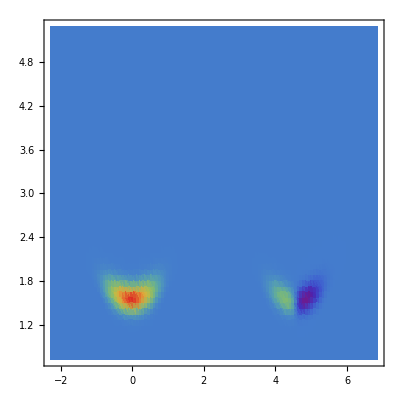
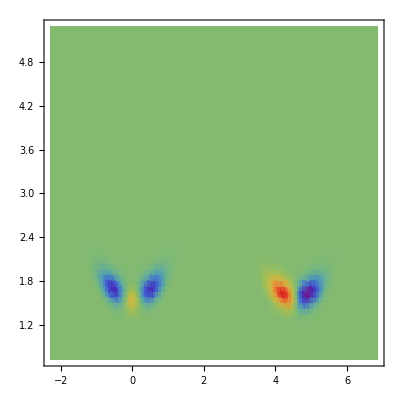
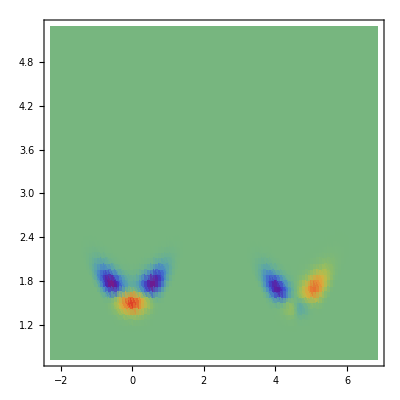
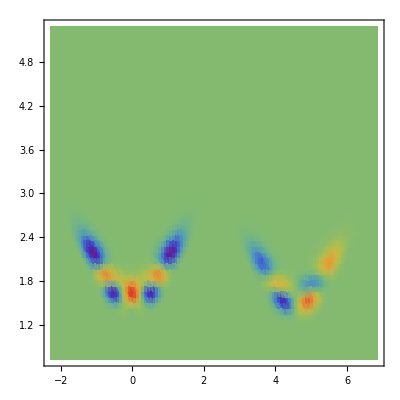

```mathematica
schloopWfns[[seriousPos]]@"Plot"["PlotMode"->"Density", "PlotDisplayMode"->"List", ColorFunction->"Rainbow"]
```

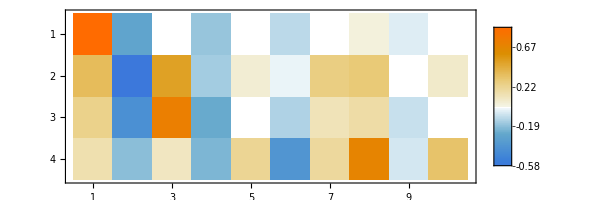

```mathematica
Show[
MatrixPlot[
Threshold[l23Coeffs[[1, seriousPos, ;;10]]^2, .001]-Threshold[l23Coeffs[[2, seriousPos, ;;10]]^2, .001],
PlotLegends->Automatic
]
]
```

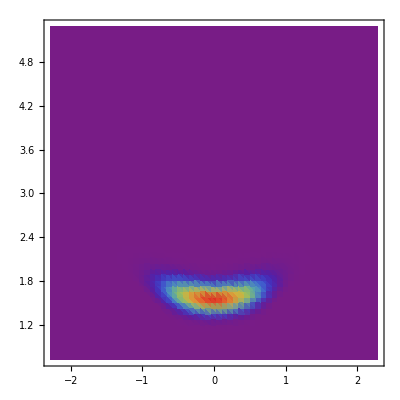
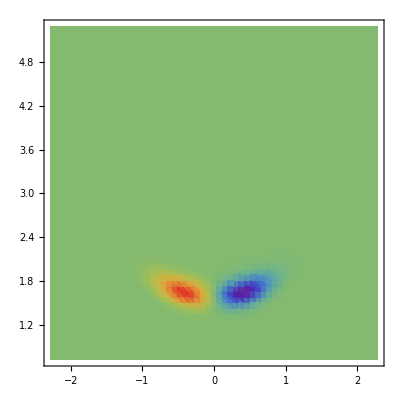
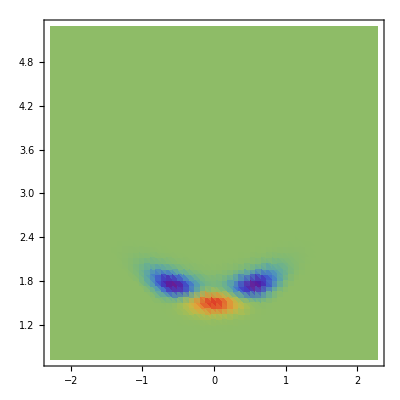
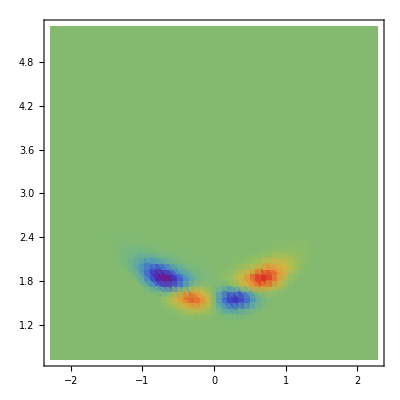
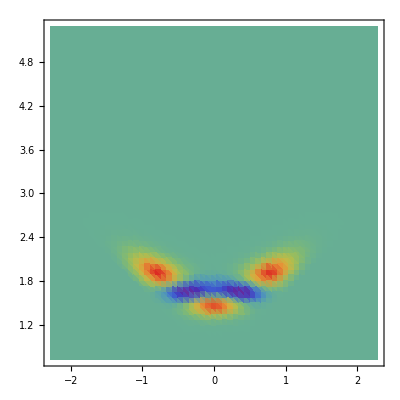
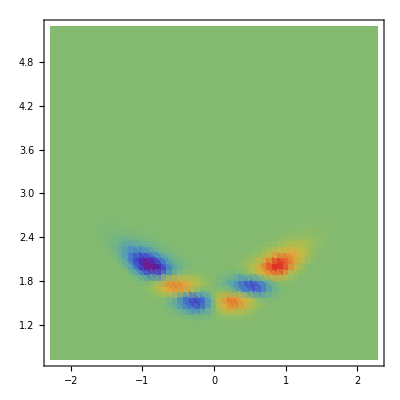
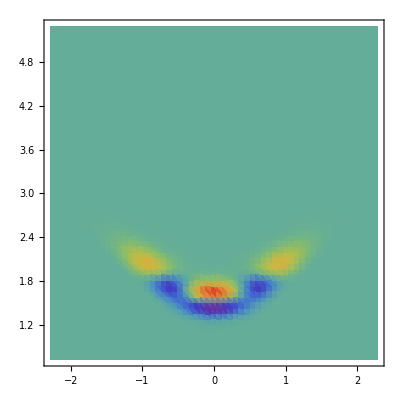
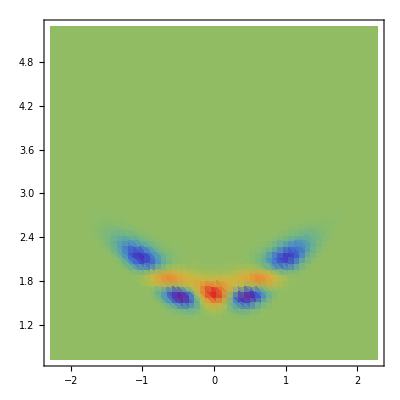

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
zeroAveragedWavefunctions[[;;10]]@"Plot"["PlotMode"->"Density", "PlotDisplayMode"->"List", ColorFunction->"Rainbow"]
```